```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Parameters*)
kmax = 30; (*SF*)
k0=2; (*SF*)
alpha=3.5; (*SF*)
alphamin=2.01; (*SF*)
alphamax=6.5; (*SF*)

nmax = 15; (*ER*)
meandeg=10; (*ER*)
meandegmin=0.1; (*ER*)
meandegmax=5; (*ER*)
threshmin=3; (*Attacks*)
threshmax=10; (*Attacks*)
```

```mathematica
(*Functions Attacks*) 
(* I do not use HeavisideTheta[x] because HeavisideTheta[0] is not defined *)
PhiHubs[k_,thresh_]:=Which[k<=thresh,1,k>thresh,0]
PhiLowDeg[k_,thresh_]:=Which[k<=thresh,0,k>thresh,1]
```

```mathematica
(*Functions SF*)
meandegreeSF[alpha_,k0_,kmax_]:=(HurwitzZeta[alpha-1,k0]-HurwitzZeta[alpha-1,kmax+1])/(HurwitzZeta[alpha,k0]-HurwitzZeta[alpha,kmax+1])
pkSF[alpha_,k0_,kmax_]:=Table[1/(HurwitzZeta[alpha,k0]-HurwitzZeta[alpha,kmax+1])i^-alpha,{i,k0,kmax}]
lhsSF:=Range[0.01,1,0.02]; 
rhsSFattacks[alpha_,k0_,kmax_,thresh_]:=Table[∑_(n=k0)^(kmax-1) (1 - PhiHubs[n+1,thresh]+PhiHubs[n+1,thresh]*1/(meandegreeSF[alpha,k0,kmax]-k0*pkSF[alpha,k0,kmax][[1]])(n+1)pkSF[alpha,k0,kmax][[n+1+1-k0]]*u^n),{u,0.01,1,0.02}];
GCSFAttacks[alpha_,k0_,kmax_,thresh_,u_]:=∑_(n=k0)^kmax (PhiHubs[n,thresh]*pkSF[alpha,k0,kmax][[n+1-k0]]*(1-u^n))
GiantComponentVsThreshSF[alpha_,k0_,kmax_,threshmin_,threshmax_]:=Table[GCSFAttacks[alpha,k0,kmax,varthresh,u]/.NSolve[u-1/(meandegreeSF[alpha,k0,kmax]-k0*pkSF[alpha,k0,kmax][[1]])∑_(n=k0)^(kmax-1) (n+1)pkSF[alpha,k0,kmax][[n+1+1-k0]](1 - PhiHubs[n+1,varthresh]+PhiHubs[n+1,varthresh]*u^n)==0 &&u<=1 && u>=0,u,Reals][[1]],{varthresh,threshmin,threshmax,1}]
GiantComponentVsAlpha[thresh_,k0_,kmax_,alphamin_,alphamax_]:=Table[GCSFAttacks[varalpha,k0,kmax,thresh,u]/.NSolve[u-1/(meandegreeSF[varalpha,k0,kmax]-k0*pkSF[varalpha,k0,kmax][[1]])∑_(n=k0)^(kmax-1) (n+1)pkSF[varalpha,k0,kmax][[n+1+1-k0]](1 -  PhiHubs[n+1,thresh]+ PhiHubs[n+1,thresh]*u^n)==0 &&u<=1 && u>=0,u,Reals][[1]],{varalpha,alphamin,alphamax,0.1}]

GCSFrandom[alpha_,k0_,kmax_,phi_,u_]:=phi*(1-∑_(n=k0)^kmax pkSF[alpha,k0,kmax][[n+1-k0]]*u^n)
GiantComponentVsPhi[alpha_,k0_,kmax_]:=Table[GCSFrandom[alpha,k0,kmax,varphi,u]/.NSolve[u-(1 - varphi+varphi*1/(meandegreeSF[alpha,k0,kmax]-k0*pkSF[alpha,k0,kmax][[1]])∑_(n=k0)^(kmax-1) (n+1)pkSF[alpha,k0,kmax][[n+1+1-k0]]*u^n)==0 &&u<=1 && u>=0,u,Reals][[1]],{varphi,0.01,1,0.01}]
```

```mathematica
(*Functions ER*)
pkER[meandeg_,nmax_]:=Table[(meandeg^i*Exp[-meandeg])/(i!)1/(∑_(k=0)^nmax (meandeg^k*Exp[-meandeg])/(k!)),{i,0,nmax}]
lhsER:=Range[0.01,1,0.02];
rhsERattacks[meandeg_,nmax_,thresh_]:=Table[∑_(n=0)^(nmax-1) 1/meandeg(n+1)pkER[meandeg,nmax][[n+1+1]]*(1 - PhiHubs[n+1,thresh]+PhiHubs[n+1,thresh]*u^n),{u,0.01,1,0.02}];
GCERattacks[meandeg_,nmax_,thresh_,u_]:=∑_(n=0)^nmax (PhiHubs[n,thresh]*pkER[meandeg,nmax][[n+1]]*(1-u^n))
GiantComponentVsThreshERattacks[meandeg_,nmax_,threshmin_,threshmax_]:=Table[GCERattacks[meandeg,nmax,varthresh,u]/.NSolve[u-∑_(n=0)^(nmax-1) 1/meandeg(n+1)pkER[meandeg,nmax][[n+1+1]](1 - PhiHubs[n+1,varthresh]+PhiHubs[n+1,varthresh]*u^n)==0 &&u<=1 && u>=0,u,Reals][[1]],{varthresh,threshmin,threshmax,1}]
GiantComponentVsMeanDegreeER[thresh_,nmax_,meandegmin_,meandegmax_]:=Table[GCERattacks[varmeandeg,nmax,thresh,u]/.NSolve[u-∑_(n=0)^(nmax-1) 1/varmeandeg(n+1)pkER[varmeandeg,nmax][[n+1+1]](1 - PhiHubs[n+1,thresh]+PhiHubs[n+1,thresh]*u^n)==0 &&u<=1 && u>=0,u,Reals][[1]],{varmeandeg,meandegmin,meandegmax,0.1}]


GCERrandom[meandeg_,nmax_,phi_,u_]:=phi*(1-∑_(n=0)^nmax pkER[meandeg,nmax][[n+1]]*u^n)
GiantComponentVsPhiER[meandeg_,nmax_]:=Table[GCERrandom[meandeg,nmax,varphi,u]/.NSolve[u-(1 - varphi+varphi*1/meandeg∑_(n=0)^(nmax-1) (n+1)pkER[meandeg,nmax][[n+1+1]]*u^n)==0 &&u<=1 && u>=0,u,Reals][[1]],{varphi,0.01,1,0.01}]
```

```mathematica
(*Comparisson of random removal vs attacks ER*)
```

```mathematica
xxERattacks=Table[N[Total[Table[pkER[meandeg,nmax][[kk+1]]*PhiHubs[kk,varthresh],{kk,0,nmax,1}]]],{varthresh,threshmin,nmax}];
yyERattacks=GiantComponentVsThreshERattacks[meandeg,nmax,threshmin,nmax];
xxSFattacks=Table[N[Total[Table[pkSF[alpha,k0,kmax][[kk+1-k0]]*PhiHubs[kk,varthresh],{kk,k0,kmax,1}]]],{varthresh,threshmin,nmax}];
yySFattacks=GiantComponentVsThreshSF[alpha,k0,kmax,threshmin,nmax];
```

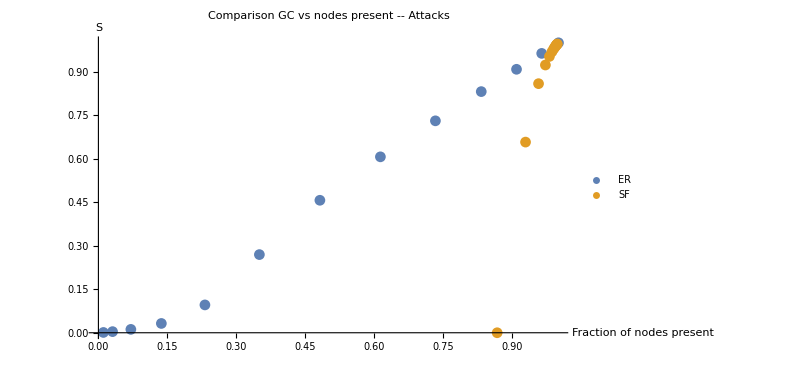

```mathematica
ListPlot[
{Transpose[{xxERattacks,yyERattacks}],Transpose[{xxSFattacks,yySFattacks}]},
AxesLabel->{"Fraction of nodes present","S"}, PlotLabel->"Comparison GC vs nodes present -- Attacks",
ImageSize->600,
PlotLegends->{"ER","SF"}
]
```

```mathematica
xxERrandom=Range[0.01,1,0.01];
yyERrandom=GiantComponentVsPhiER[meandeg,nmax];
xxSFrandom=Range[0.01,1,0.01];
yySFrandom=GiantComponentVsPhi[alpha,k0,kmax];
```

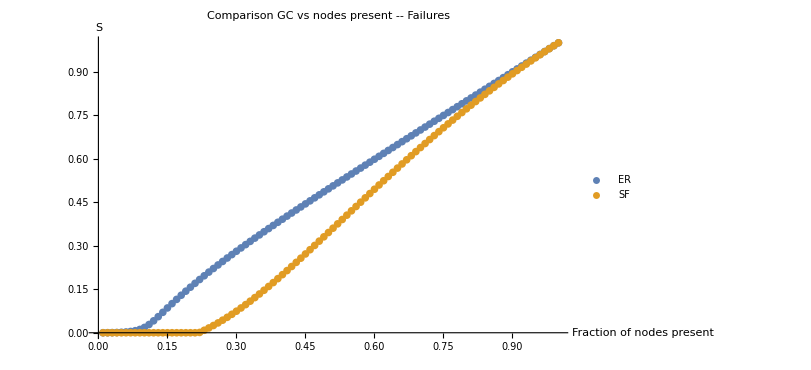

```mathematica
ListPlot[
{Transpose[{xxERrandom,yyERrandom}],Transpose[{xxSFrandom,yySFrandom}]},
AxesLabel->{"Fraction of nodes present","S"}, PlotLabel->"Comparison GC vs nodes present -- Failures",
ImageSize->600,
PlotLegends->{"ER","SF"}
]
```